```mathematica
(*the data is read from figures, instead of copy from data file*)
```

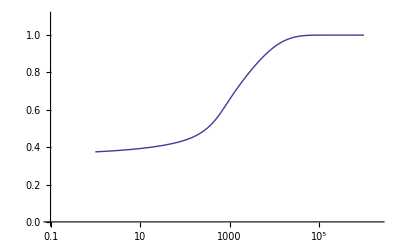

```mathematica
ListLogLinearPlot[{{1,60/160},{100,70/160},{1000,105/160},{10000,150/160},{100000,160/160},{1000000,160/160}},PlotRange->{{0.1,2000000},{0,1.1}},InterpolationOrder -> 3, Joined -> True, PlotStyle-> Thick]
```

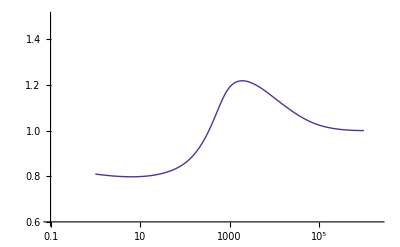

```mathematica
ListLogLinearPlot[{{1,170/210},{100,180/210},{1000,250/210},{10000,240/210},{100000,215/210},{1000000,210/210}},PlotRange->{{0.1,2000000},{0.6,1.5}},InterpolationOrder -> 3, Joined -> True,PlotStyle-> Thick]
```

```mathematica
orin = {0,0};
r = 1.0;
r1 = 0.75;
size = 40;
length = 2.0;
del = r+r+length;
```

# Crash Model

## Bernolli model

```mathematica
Node[orin_,r_,text_,size_,length_,r1_,text2_]:= {
{Thick,Circle[orin,r]},
Text[Style[text,size],orin],
{Thick,Arrowheads[.05],Arrow[{{orin⟦1⟧+r,orin⟦2⟧},{orin⟦1⟧+r + length,orin⟦2⟧}}]},
(*{Thick,Circle[orin+{(r+r1/2)*Sin[0],(r+r1/2)*Cos[0]},{0.5,1.0}]}*)
Text[Style[text2,size/1.5],orin+{r+length/2,0},{0,-1}]
}
```

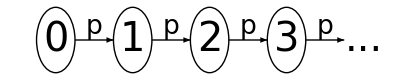

```mathematica
Graphics[{
Node[{0,0},r,"0",size,length,r1,"p"],
Node[{del,0},r,"1",size,length,r1,"p"],
Node[{2*del,0},r,"2",size,length,r1,"p"],
Node[{3*del,0},r,"3",size,length,r1,"p"],
Text[Style["...",size],{4*del,0}]
}]
```

```mathematica
NodeNew[orin_,r_,text_,size_,length_,r1_,text2_]:= {
{Thick,Circle[orin,r]},
Text[Style[text,size],orin],
{Thick,Arrowheads[.05],Arrow[{{orin⟦1⟧-r - length,orin⟦2⟧},{orin⟦1⟧-r,orin⟦2⟧}}]},
(*{Thick,Circle[orin+{(r+r1/2)*Sin[0],(r+r1/2)*Cos[0]},{0.5,1.0}]}*)
Text[Style[text2,size/1.5],orin-{r+length/2,0},{0,-1}]
}
```

3.

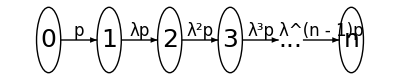

```mathematica
sizex = 25;
length1 = 3.0
del1  = r+r + length1;
Graphics[{
Node[{0,0},r,"0",sizex,length1,r1,"p"],
Node[{del1,0},r,"1",sizex,length1,r1,"λp"],
Node[{2*del1,0},r,"2",sizex,length1,r1,"λ^2p"],
Node[{3*del1,0},r,"3",sizex,length1,r1,"λ^3p"],
Text[Style["...",sizex],{4*del1,0}],
NodeNew[{5*del1,0},r,"n",sizex,length1,r1,"λ^(n - 1)p"]
}]
```